numeric simulation

```mathematica
Quit[]
```

```mathematica
dispSimp = {a_[t]->a,Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]};
```

original equations:

```mathematica
(quadEqNominal=EulerEquations[L,{(*Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],*)Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p x_p''(t)
(k_1 (-1/2 h_p cos(θ_p(t))+1/2 l_p sin(θ_p(t))-y_p(t)+y_1(t)) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (-1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))-y_p(t)+y_2(t)) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==m_p (g+y_p''(t))
ⅈ_(p,zz) θ_p''(t)+(k_1 (h_p (x_1(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_1(t)-y_p(t)) sin(θ_p(t)))+l_p (x_1(t) (-sin(θ_p(t)))+x_p(t) sin(θ_p(t))+(y_1(t)-y_p(t)) cos(θ_p(t)))) (√(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(2 √(1/4 (h_p sin(θ_p(t))+l_p cos(θ_p(t))-2 x_p(t)+2 x_1(t))^2+(1/2 h_p cos(θ_p(t))-1/2 l_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+l_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2)-L0_2))/(2 √((1/2 h_p sin(θ_p(t))-1/2 l_p cos(θ_p(t))-x_p(t)+x_2(t))^2+1/4 (h_p cos(θ_p(t))+l_p sin(θ_p(t))+2 y_p(t)-2 y_2(t))^2))==0)

```mathematica
non-conserving forces:
aerodynamic =  f(OverDot[Subscript[x, p]],OverDot[Subscript[y, p]],Subscript[θ, p], Subscript[w, x],Subscript[w, y]) , w for wind components. = f(Subscript[relV, x],Subscript[relV, y]) , relV is relative to air 
dumping (structural)= f(OverDot[Subscript[l, i]])=f(OverDot[Subscript[x, i]],OverDot[Subscript[y, i]],OverDot[Subscript[x, p]],OverDot[Subscript[y, p]])
```

non dim the full equations

```mathematica
(smallEqs=quadEqNominal/.terms2/.terms3)//MatrixForm
```

((r1x k_1 (a-L0_1))/(√(a^2))+(r2x k_2 (b-L0_2))/(√(b^2))==m_p x_p''[t]
(r1y k_1 (a-L0_1))/(√(a^2))+(r2y k_2 (b-L0_2))/(√(b^2))==m_p (g+y_p''[t])
(c1 k_1 (a-L0_1))/(√(a^2))+(c2 k_2 (b-L0_2))/(√(b^2))+ⅈ_(p,zz) θ_p''[t]==0)

NonDimEq manually settings the terms:

```mathematica
OverTilde[Subscript[y, p]][t]=Subscript[y, p][t] /Subscript[L0, 1]  or any other of the lengths varialbes (Subscript[x, p],r1x,r1y,r2x,r2y,Subscript[h, p],Subscript[l, p])
t=τ/Subscript[ω, s]
Subscript[ω, s]^2=(Subscript[k, 1]/Subscript[m, p])[g/l=1/s^2]
A is non-dimentional  form of 'a'
B is non-dimentional  form of 'b'
```

(((1-1/A) k_1 L0_1 r1x)/m_p+(k_2 L0_1 r2x (1-L0_2/(B L0_1)))/m_p==L0_1 ω_s^2 x_p''(t)
((1-1/A) k_1 L0_1 r1y)/m_p+(k_2 L0_1 r2y (1-L0_2/(B L0_1)))/m_p-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 k_2 L0_1^2 (1-L0_2/(B L0_1)))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
(*Subscript[Delta, Equilibrium]=(Subscript[m, p] g)/Subscript[k, i]*)
```

```mathematica
greekTerms={
Subscript[k, 2]/Subscript[k, 1]->κ,
Subscript[L0, 2]/Subscript[L0, 1]->ℒ,
Subscript[k, 1]/Subscript[m, p]->Subscript[ω, s]^2,
(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->α,
g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))->γ
}
```

```mathematica
(NonDimEq={
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1x +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2x ==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[x, p]''[t],
Subscript[ω, s]^2 Subscript[L0, 1](1-1/A)r1y +κ Subscript[ω, s]^2  Subscript[L0, 1](1-1/B ℒ)r2y -g/(Subscript[L0, 1] Subscript[ω, s]^2)Subscript[L0, 1] Subscript[ω, s]^2==Subscript[L0, 1] Subscript[ω, s]^2 Subscript[y, p]''[t],
Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/A)Subscript[c, 1] +κ Subscript[k, 1]/(-Subscript[ⅈ, p,zz]) Subscript[L0, 1]^2/Subscript[ω, s]^2 Subscript[ω, s]^2(1-1/B ℒ)Subscript[c, 2]==Subscript[ω, s]^2 Subscript[θ, p]''[t]
})//Flatten//MatrixForm//TraditionalForm
```

((1-1/A) L0_1 r1x ω_s^2+κ L0_1 r2x (1-ℒ/B) ω_s^2==L0_1 ω_s^2 x_p''(t)
(1-1/A) L0_1 r1y ω_s^2+κ L0_1 r2y (1-ℒ/B) ω_s^2-g==L0_1 ω_s^2 y_p''(t)
-((1-1/A) c_1 k_1 L0_1^2)/(ⅈ_(p,zz))-(c_2 κ k_1 L0_1^2 (1-ℒ/B))/(ⅈ_(p,zz))==ω_s^2 θ_p''(t))

```mathematica
𝒳^(..)=({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)Subscript[𝒱, 1]+κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)Subscript[𝒱, 2]-({{0}, {γ}, {0}})-Cmat.𝒳̇+Forces
```

```mathematica
𝒳^(..)=f[𝒳,𝒳̇]
```

```mathematica
Quit[]
```

```mathematica
𝒳=({{Subscript[x, p][t]}, {Subscript[y, p][t]}, {Subscript[θ, p][t]}})(*//Flatten*)
greekTermsSymetricCase={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1
}
greekTermsGeneral={
(*Subscript[k, 2]/Subscript[k, 1]->*)κ->1,
(*Subscript[L0, 2]/Subscript[L0, 1]->*)ℒ->1,
(*Subscript[k, 1]/Subscript[m, p]->*)Subscript[ω, s]^2->1,
(*(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p](=(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2))->*)α->1,
(*g/(Subscript[L0, 1] Subscript[ω, s]^2)(=(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))-> *)γ->1 (* make sure it is not over-determined constant *)

}
(* already here : replacing all former Subscript[h, p],Subscript[l, p] with new 2 Subscript[h, p],2 Subscript[l, p]*)
A(*->√(r1x^2+r1y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))^2)

B(*->√(r2x^2+r2y^2)*)=√((Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))^2+(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))^2)
(*Subscript[c, 1](*->dr1+dr2*)=Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))
Subscript[c, 2](*->dr3+dr4*)=Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))*)
Subscript[𝒱, 1](*=({{r1x}, {r1y}, {Subscript[c, 1]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 1][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]+ Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 1][t]-Subscript[y, p][t]))}, {Subscript[l, p] (-Sin[Subscript[θ, p][t]] (Subscript[x, 1][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 1][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 1][t]-Subscript[y, p][t]))}})
Subscript[𝒱, 2](*=({{r2x}, {r2y}, {Subscript[c, 2]}})*)=({{(Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[x, 2][t]-Subscript[x, p][t]))}, {(- Cos[Subscript[θ, p][t]] Subscript[h, p]- Sin[Subscript[θ, p][t]] Subscript[l, p]+(Subscript[y, 2][t]-Subscript[y, p][t]))}, {Subscript[l, p] (Sin[Subscript[θ, p][t]] (Subscript[x, 2][t]- Subscript[x, p][t])+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))+Subscript[h, p] (Cos[Subscript[θ, p][t]]( Subscript[x, 2][t]- Subscript[x, p][t])+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))}})
Cmat=({{Subscript[c, 1], 0, 0}, {0, Subscript[c, 2], 0}, {0, 0, Subscript[c, 3]}});
nameChange={Subscript[l, p]->Subscript[w, p]};
"equations with no general forces :"
EOM=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/A)).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, 1, 0}, {0, 0, -α}})(1-1/B ℒ)).Subscript[𝒱, 2]-({{0}, {γ}, {0}})-Cmat.D[𝒳,{t,1}]  //.nameChange//Flatten;
```

{{x_p[t]},{y_p[t]},{θ_p[t]}}

{κ→1,ℒ→1}

{κ→1,ℒ→1,ω_s^2→1,α→1,γ→1}

√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t])^2)

√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t])^2)

{{Sin[θ_p[t]] h_p+Cos[θ_p[t]] l_p+x_1[t]-x_p[t]},{-Cos[θ_p[t]] h_p+Sin[θ_p[t]] l_p+y_1[t]-y_p[t]},{l_p (-Sin[θ_p[t]] (x_1[t]-x_p[t])+Cos[θ_p[t]] (y_1[t]-y_p[t]))+h_p (Cos[θ_p[t]] (x_1[t]-x_p[t])+Sin[θ_p[t]] (y_1[t]-y_p[t]))}}

{{Sin[θ_p[t]] h_p-Cos[θ_p[t]] l_p+x_2[t]-x_p[t]},{-Cos[θ_p[t]] h_p-Sin[θ_p[t]] l_p+y_2[t]-y_p[t]},{h_p (Cos[θ_p[t]] (x_2[t]-x_p[t])+Sin[θ_p[t]] (y_2[t]-y_p[t]))+l_p (Sin[θ_p[t]] (x_2[t]-x_p[t])+Cos[θ_p[t]] (-y_2[t]+y_p[t]))}}

equations with no general forces :

```mathematica
Clear[a]
```

```mathematica
dispNoTime={aa_[t]->aa};(*
EOM/.dispNoTime/.greekTermsSymetricCase//Flatten(*//MatrixForm*)(*//TraditionalForm*);
EOM/.dispNoTime/.greekTermsSymetricCase//Flatten(*//MatrixForm*)//TraditionalForm*)
```

```mathematica
(*numerics={Subscript[h, p]->0.1,Subscript[w, p]->1,Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0,α->0.04,γ->2}*)
(*EOM//.greekTermsSymetricCase//.numerics//Flatten//TraditionalForm*)
```

{h_p→0.1,w_p→1,x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0,α→0.04,γ→2}

(x_p''(t)
y_p''(t)
θ_p''(t))==((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2) (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2)))+(cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)) (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2)))
(1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))+(1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))-2
-0.04 (1-1/(√((-cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t)+2)^2+(-0.1 cos(θ_p(t))-sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) (2-x_p(t))+cos(θ_p(t)) y_p(t)+0.1 (cos(θ_p(t)) (2-x_p(t))-sin(θ_p(t)) y_p(t)))-0.04 (1-1/(√((cos(θ_p(t))+0.1 sin(θ_p(t))-x_p(t))^2+(-0.1 cos(θ_p(t))+sin(θ_p(t))-y_p(t))^2))) (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t)+0.1 (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t))))

```mathematica
(*EquibInputConditions={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}*)
```

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→y_1[t]}

```mathematica
(*(SymetricEquib=EOM/.nameChange/.greekTermsSymetricCase(*/.equibTerms*)//.EquibInputConditions)//MatrixForm//TraditionalForm*)
```

(x_p''(t)
y_p''(t)
θ_p''(t))==((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2)))+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2)))-c_1 x_p'(t)
-γ+(1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))+(1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))-c_2 y_p'(t)
-α (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+2 w_p-x_p(t))^2+(-cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) (2 w_p-x_p(t))+cos(θ_p(t)) y_p(t))+h_p (cos(θ_p(t)) (2 w_p-x_p(t))-sin(θ_p(t)) y_p(t)))-α (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p-x_p(t))^2+(-cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_p(t))^2))) (w_p (sin(θ_p(t)) x_p(t)-cos(θ_p(t)) y_p(t))+h_p (-cos(θ_p(t)) x_p(t)-sin(θ_p(t)) y_p(t)))-c_3 θ_p'(t))

```mathematica
NumericParametersTest={Subscript[k, 1]->200, Subscript[k, 2]->Subscript[k, 1]+0,Subscript[L0, 1]->2,Subscript[L0, 2]->Subscript[L0, 1]+0,Subscript[m, p]->2,Subscript[h, p]->0.1,Subscript[w, p]->1,g->9.81}
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->0(*,α->0.04,γ->2*)}
cFactor=0.1;
NumericStructuralDamping={Subscript[c, 1]->cFactor,Subscript[c, 2]->cFactor,Subscript[c, 3]->cFactor};
NumericNonStructuralDamping={Subscript[c, 1]->0,Subscript[c, 2]->0,Subscript[c, 3]->0};
greekTermsGeneralForTest={
κ->Subscript[k, 2]/Subscript[k, 1],
ℒ->Subscript[L0, 2]/Subscript[L0, 1],
Subscript[ω, s]^2->Subscript[k, 1]/Subscript[m, p],
α->(3 Subscript[L0, 1]^2)/(Subscript[w, p]^2+Subscript[h, p]^2),
γ->((g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1]))
}
(*g/Subscript[L0, 1]/.NumericParametersTest*)
NumericTestParams=greekTermsGeneralForTest//.NumericParametersTest
```

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

{κ→k_2/k_1,ℒ→L0_2/L0_1,ω_s^2→k_1/m_p,α→(3 L0_1^2)/(h_p^2+w_p^2),γ→(g m_p)/(k_1 L0_1)}

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

“(*simple case testings:*)”

```mathematica
(*trajectory:
τ=0: y^(..)=1m/s^2  until Subscript[y, 1]=Subscript[y, 2]=10 Subscript[L0, 1]
    y^(..)=-1m/s^2 until OverDot[Subscript[y, 1]]=OverDot[Subscript[y, 2]]=0
Subscript[x, 1]^(..)=Subscript[x, 2]^(..)=1m/s^2  until OverDot[Subscript[x, 1]]=OverDot[Subscript[x, 2]]=2m/s
disterbunce can be input by Subscript[x, 1]+=5 Subscript[L0, 1] over 1/(100 √Subscript[ω, s])*)
```

```mathematica
(* greekTermsSymetricCase must be used again because this is where the equilibrium point is refering to .
EquibInputConditions might be turned of later for better investigation *)
(SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.NumericEquibInputs)/.dispNoTime//MatrixForm//TraditionalForm
```

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2)))+(sin(θ_p) h_p+cos(θ_p) w_p-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-c_1 x_p'
-γ+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (-cos(θ_p) h_p-sin(θ_p) w_p-y_p)+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (-cos(θ_p) h_p+sin(θ_p) w_p-y_p)-c_2 y_p'
-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) (2 w_p-x_p)+cos(θ_p) y_p)+h_p (cos(θ_p) (2 w_p-x_p)-sin(θ_p) y_p))-α (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (w_p (sin(θ_p) x_p-cos(θ_p) y_p)+h_p (-cos(θ_p) x_p-sin(θ_p) y_p))-c_3 θ_p')

```mathematica
testValid={Subscript[x, p][t]->1,Subscript[y, p][t]->1,Subscript[θ, p][t]->1};
(*testValid={Subscript[x, p][t]->1,(*Subscript[y, p][t]->1,*)Subscript[θ, p][t]->1};*)
"equation with 'testValid' applied in print only:"
(EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericNonStructuralDamping)/.testValid//MatrixForm//TraditionalForm
EOMtoSolve;
numericEqs={X1'[t]==X2[t],
X2'[t]== (EOMtoSolve[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (EOMtoSolve[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (EOMtoSolve[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];
NumericTestParams
NumericParametersTest
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.1,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0.1}/.NumericTestParams/.NumericParametersTest*)
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.001,X5[0]==0,X6[0]==1}/.NumericTestParams/.NumericParametersTest*)
(*startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0}/.NumericTestParams/.NumericParametersTest*)
startValues={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==1,X5[0]==0,X6[0]==0}/.NumericTestParams/.NumericParametersTest
T=100
sol1 = NDSolve[ {numericEqs, startValues}, {X1, X2,X3,X4,X5,X6}, {t, 0, T} ]
```

equation with 'testValid' applied in print only:

(x_p''(t)
y_p''(t)
θ_p''(t))==(0.762781
-0.703322
-5.36449)

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{X1[0]==1,X2[0]==0.001,X3[0]==-1.12453,X4[0]==1,X5[0]==0,X6[0]==0}

100

{{X1→InterpolatingFunction[{{0., 100.}}, <>],X2→InterpolatingFunction[{{0., 100.}}, <>],X3→InterpolatingFunction[{{0., 100.}}, <>],X4→InterpolatingFunction[{{0., 100.}}, <>],X5→InterpolatingFunction[{{0., 100.}}, <>],X6→InterpolatingFunction[{{0., 100.}}, <>]}}

```mathematica
EquibInputConditions
NumericEquibInputs
```

EquibInputConditions

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

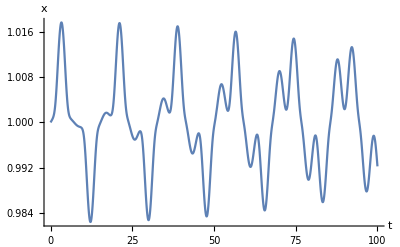
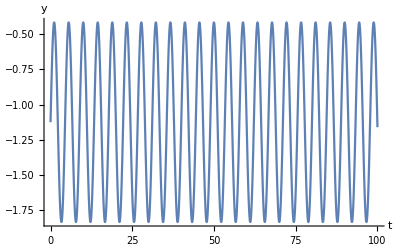
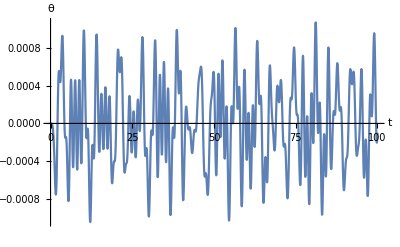

```mathematica
{Plot[{X1[t]}/.sol1,{t,0,T},AxesLabel->{"t","x"},PlotRange->All],
Plot[{X3[t]}/.sol1,{t,0,T},AxesLabel->{"t","y"},PlotRange->All],
Plot[{X5[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ"},PlotRange->All]}
```

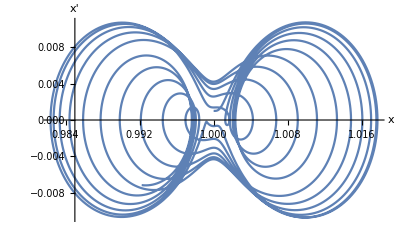
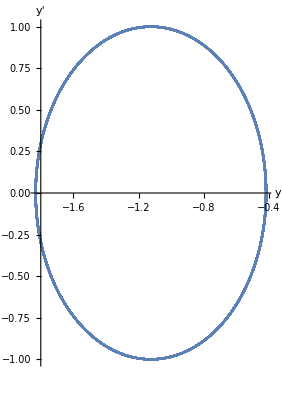
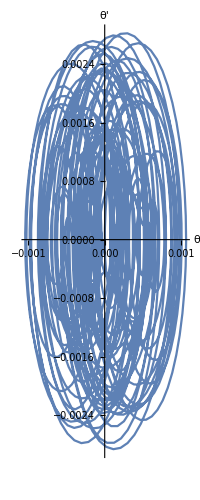

```mathematica
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,T},AxesLabel->{"x","x'"}],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,T},AxesLabel->{"y","y'"}],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,T},AxesLabel->{"θ","θ'"}]}
(*DrawAnimation*)
Animate[DrawSystem[Subscript[x, 1],Subscript[y, 1],Subscript[x, 2],Subscript[y, 2],Subscript[x, p],Subscript[y, p],θp,Subscript[w, p]][[1]]/.({(Subscript[x, p]->X1[t]/.sol1)[[1]],(Subscript[y, p]->X3[t]/.sol1)[[1]],(θp->X5[t]/.sol1)[[1]],Subscript[x, 1]->0,
Subscript[x, 2]->2 Subscript[w, p],Subscript[y, 1]->0,Subscript[y, 2]->0,NumericEquibInputs}//Flatten)(*/.EquibInputConditions*)/.NumericParametersTest,{t,0,T}]
```

```mathematica
(*dataset=Flatten[Table[{x,y,f[x,y]},{x,0,1,.1},{y,0,1.1}],1]*)
(*Export["mydataset.txt",dataset,"CSV"]*)
(*dataset=Flatten[Table[{t,X1[t]}/.sol1,{t,0,T}],1]
dataset=Flatten[Table[{t,X1[t]}/.sol1,{t,0,T,0.01}],1];*)
datasetAllState=Flatten[Table[
{t,X1[t],X2[t],X3[t],X4[t],X5[t],X6[t]}/.sol1,
{t,0,T,0.01}],1];
(*Export["./GitHub/quad_docs/mydataset.csv",dataset]*)
Export["./GitHub/quad_docs/myDatasetAllState.csv",datasetAllState]
```

./GitHub/quad_docs/myDatasetAllState.csv

```mathematica
ListPlot[dataset]
```

```mathematica
add both a driving force and damping
```

```mathematica
NumericTestParams
NumericParametersTest
EquibInputConditions
NumericEquibInputs
NumericStructuralDamping
```

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

EquibInputConditions

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p,y_2[t]→0}

{c_1→0.01,c_2→0.01,c_3→0.01}

```mathematica
Ω=2; (* Hz *)
Fmag=0.82 (*NonDim magnitude*)
Fmag=0
Fmag=0.005
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0+Fmag Sin[Ω t],Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}
(SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.NumericEquibInputs)/.dispNoTime//MatrixForm//TraditionalForm
EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericStructuralDamping;
```

0.82

0

0.005

{x_1[t]→0,y_1[t]→0.005 Sin[2 t],x_2[t]→2 w_p,y_2[t]→y_1[t]}

(x_p''
y_p''
θ_p'')==((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p) (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2)))+(sin(θ_p) h_p+cos(θ_p) w_p-x_p) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-c_1 x_p'
-γ+(1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)+(1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2))) (0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)-c_2 y_p'
-α (w_p (sin(θ_p) x_p+cos(θ_p) (0.005 sin(2 t)-y_p))+h_p (sin(θ_p) (0.005 sin(2 t)-y_p)-cos(θ_p) x_p)) (1-1/(√((sin(θ_p) h_p+cos(θ_p) w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p+sin(θ_p) w_p-y_p)^2)))-α (1-1/(√((sin(θ_p) h_p-cos(θ_p) w_p+2 w_p-x_p)^2+(0.005 sin(2 t)-cos(θ_p) h_p-sin(θ_p) w_p-y_p)^2))) (h_p (cos(θ_p) (2 w_p-x_p)+sin(θ_p) (0.005 sin(2 t)-y_p))+w_p (sin(θ_p) (2 w_p-x_p)+cos(θ_p) (y_p-0.005 sin(2 t))))-c_3 θ_p')

```mathematica
NumericTestParams
NumericParametersTest
startValuesWithMove={X1[0]==Subscript[w, p],X2[0]==0.001,X3[0]==-1-Subscript[h, p]-γ/2,X4[0]==0.01,X5[0]==0,X6[0]==0.001}/.NumericTestParams/.NumericParametersTest
startValuesFromStatic={X1[0]==Subscript[w, p],X2[0]==0.00,X3[0]==-1-Subscript[h, p]-1/2 γ,X4[0]==0.0,X5[0]==0,X6[0]==0.00}/.NumericTestParams/.NumericParametersTest
```

{κ→1,ℒ→1,ω_s^2→100,α→11.8812,γ→0.04905}

{k_1→200,k_2→k_1,L0_1→2,L0_2→L0_1,m_p→2,h_p→0.1,w_p→1,g→9.81}

{X1[0]==1,X2[0]==0.001,X3[0]==-1.12453,X4[0]==0.01,X5[0]==0,X6[0]==0.001}

{X1[0]==1,X2[0]==0.,X3[0]==-1.12453,X4[0]==0.,X5[0]==0,X6[0]==0.}

```mathematica
startValuesFromStatic[[1]]
```

X1[0]==1

```mathematica
"Because of energy conservation one can clearly never get chaos from the motion of a single degree of freedom. We therefore add both a driving force and damping, in order to remove energy conservation"
```

```mathematica
Ω=2; (* Hz *);
calcSol[Fmag_,T_,startValues_ (*vec of 6*)]:={
NumericEquibInputs={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0+Fmag Sin[Ω t],Subscript[x, 2][t]->2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]};
SymetricEOMtoInvestigate=EOM/.greekTermsSymetricCase//.NumericEquibInputs;
EOMtoSolve=SymetricEOMtoInvestigate/.NumericTestParams/.NumericParametersTest/.NumericStructuralDamping;

numericEqs={X1'[t]==X2[t],
X2'[t]== (EOMtoSolve[[2,1]][[1]]),
X3'[t]==X4[t],
X4'[t]== (EOMtoSolve[[2,2]][[1]]),
X5'[t]==X6[t],
X6'[t]== (EOMtoSolve[[2,3]][[1]])}/.Subscript[x, p][t]->X1[t]/.Subscript[y, p][t]->X3[t]/.Subscript[θ, p][t]->X5[t]/.D[Subscript[x, p][t],t]->X2[t]/.D[Subscript[y, p][t],t]->X4[t]/.D[Subscript[θ, p][t],t]->X6[t];

(*startValues=startValuesFromStatic;*)
(*startValues=startValuesWithMove;*)
(*Print["startValues : "];
Print[startValues];*)
initValuesEquations={X1[0]==startValues[[1]],X2[0]==startValues[[2]],X3[0]==startValues[[3]],					X4[0]==startValues[[4]],X5[0]==startValues[[5]],X6[0]==startValues[[6]]};

sol1 = NDSolve[ {numericEqs, initValuesEquations}, {X1, X2,X3,X4,X5,X6}, {t, 0, T},MaxSteps -> Floor[1000*T] ];
sol1[[1]]  (* the value/data to return *)
}
```

according to ref of Duffing.nb:

```mathematica
"Rainbow: blue color is the beginning ,  as from 0 (blue) to 1 (red/orange)"
```

```mathematica
plotParametricPlots[midT_]:={
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,0,midT},AxesLabel->{"x","x'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,0,midT},AxesLabel->{"y","y'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,0,midT},AxesLabel->{"θ","θ'"},PlotRange->All,ColorFunction->"Rainbow"]},
{ParametricPlot[{X1[t],X2[t]}/.sol1,{t,midT,T},AxesLabel->{"x","x'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X3[t],X4[t]}/.sol1,{t,midT,T},AxesLabel->{"y","y'"},PlotRange->All,ColorFunction->"Rainbow"],
ParametricPlot[{X5[t],X6[t]}/.sol1,{t,midT,T},AxesLabel->{"θ","θ'"},PlotRange->All,ColorFunction->"Rainbow"]},
{Plot[{X1[t]}/.sol1,{t,0,T},AxesLabel->{"t","x"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X2[t]}/.sol1,{t,0,T},AxesLabel->{"t","x'"},PlotRange->All(*,ColorFunction->"Rainbow"*)],
Plot[{X3[t]}/.sol1,{t,0,T},AxesLabel->{"t","y"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X4[t]}/.sol1,{t,0,T},AxesLabel->{"t","y'"},PlotRange->All(*,ColorFunction->"Rainbow"*)],
Plot[{X5[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ"},PlotRange->All,ColorFunction->"Rainbow"],
Plot[{X6[t]}/.sol1,{t,0,T},AxesLabel->{"t","θ'"},PlotRange->All(*,ColorFunction->"Rainbow"*)]}
}
```

```mathematica
{"expectedPeriod by Forcing period:" ,
 expectedPeriod=2π/(Ω /Subscript[ω, s])  /.(Subscript[ω, s]->√(Subscript[ω, s]^2)/.NumericTestParams)//N,"[sec]"}
```

{expectedPeriod by Forcing period:,31.4159,[sec]}

```mathematica
T=1*expectedPeriod
sectionTime=9/10 T;
```

31.4159

{{X1→InterpolatingFunction[{{0., 314.159}}, <>],X2→InterpolatingFunction[{{0., 314.159}}, <>],X3→InterpolatingFunction[{{0., 314.159}}, <>],X4→InterpolatingFunction[{{0., 314.159}}, <>],X5→InterpolatingFunction[{{0., 314.159}}, <>],X6→InterpolatingFunction[{{0., 314.159}}, <>]}}

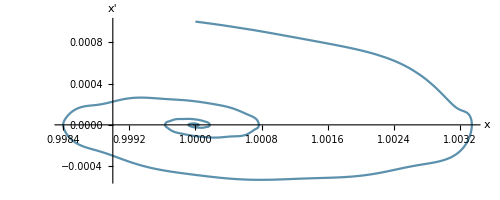
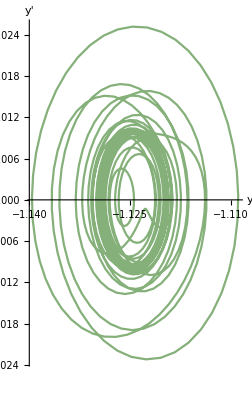
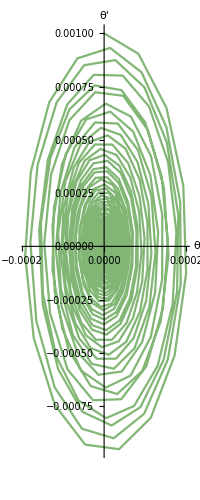
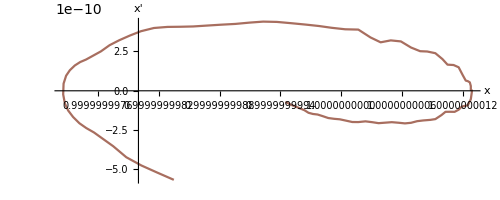
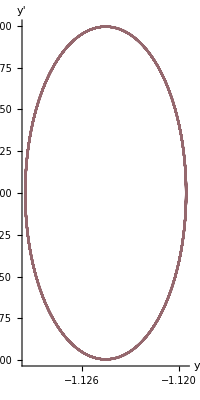
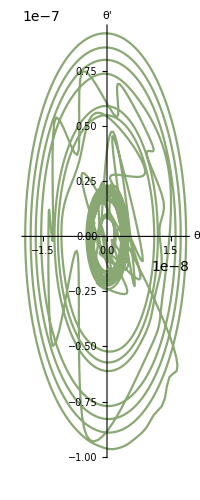
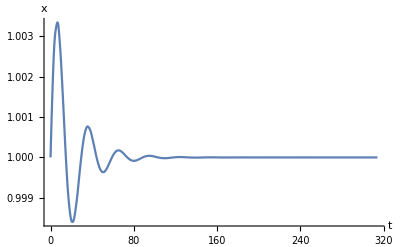
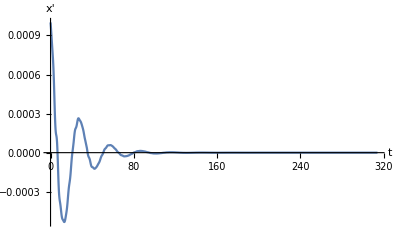

```mathematica
(*sol1 = NDSolve[ {numericEqs, startValues}, {X1, X2,X3,X4,X5,X6}, {t, 0, T} , MaxSteps -> 117500 ]*)
(*calcSol[0.005, T,startValuesWithMove[[All,2]]]
plotParametricPlots[sectionTime]*)
```

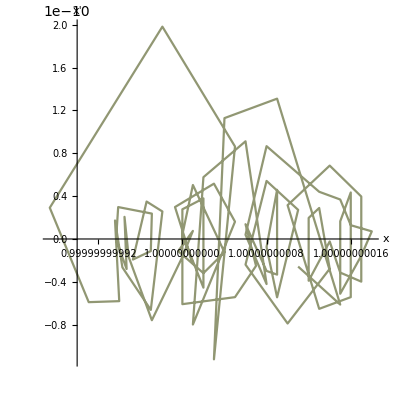
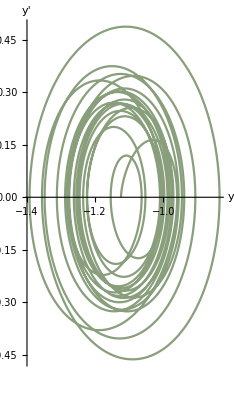
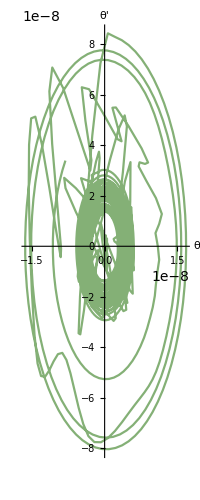
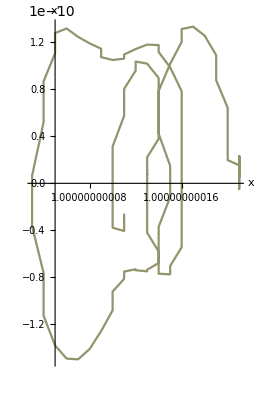
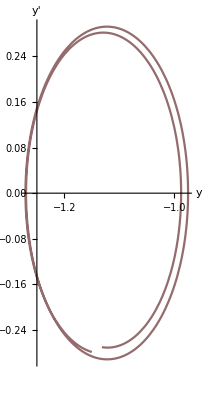
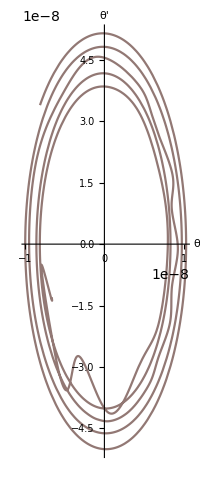
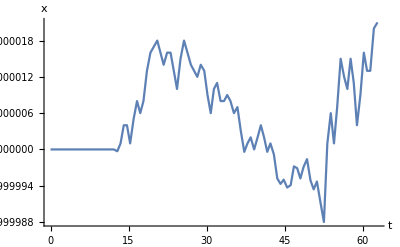
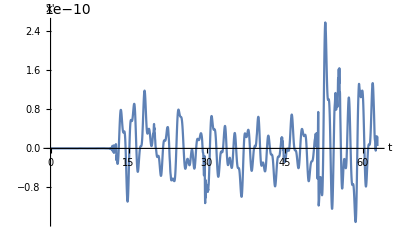

```mathematica
calcSol[0.14, T,startValuesFromStatic[[All,2]]];plotParametricPlots[sectionTime]
calcSol[0.16, T,startValuesFromStatic[[All,2]]];plotParametricPlots[sectionTime]
Manipulate[calcSol[f, T,startValuesFromStatic[[All,2]]];plotParametricPlots[sectionTime],{f,0.01,0.5}]
```

```mathematica
poincare[d_,ndrop_,nplot_,psize_]:=(
gg[prevStartValues_]:=({X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]}/.calcSol[d, T,prevStartValues])[[1]];
(*Print[calcSol[d, T,startValuesFromStatic]];*)
(*Print[gg[startValuesFromStatic[[All,2]]]];*)
extList=Drop[NestList[gg,startValuesFromStatic[[All,2]],nplot+ndrop],ndrop];
(*Print[extList];*)
pX=ListPlot[Transpose[{extList[[All,1]],extList[[All,2]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","x'"}];
pY=ListPlot[Transpose[{extList[[All,3]],extList[[All,4]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"y","y'"}];
pθ=ListPlot[Transpose[{extList[[All,5]],extList[[All,6]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","θ'"}];
{pX,pY,pθ}
)
```

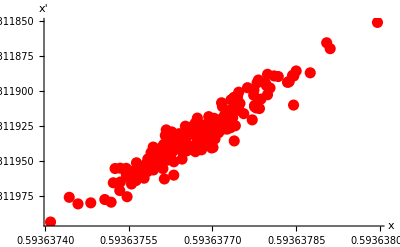
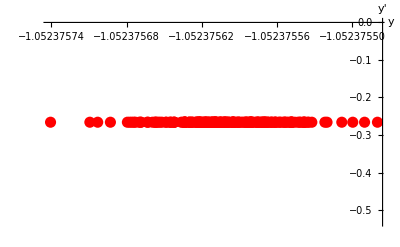
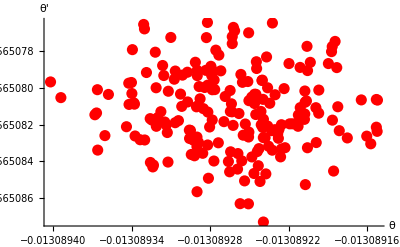

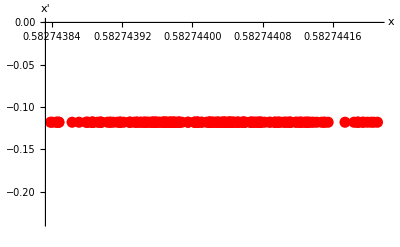
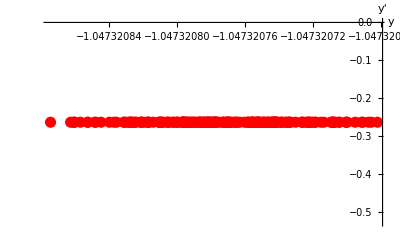
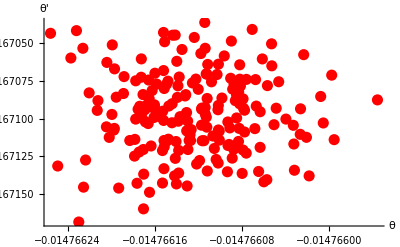

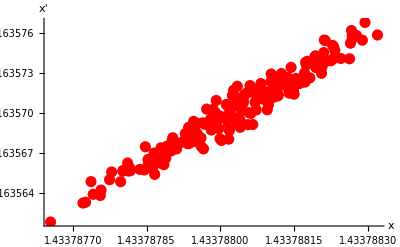
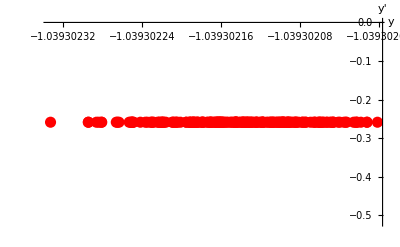

```mathematica
(*poincare[0.14,100,200,0.02]*)
poincare[0.161,100,200,0.02]
poincare[0.1612,100,200,0.02]
poincare[0.1614,100,200,0.02]
```

```mathematica
(*bifurcation[dmin_,dmax_,nd_,xmin_,xmax_,γ_,ω_,ndrop_,nplot_,psize_]:=(
xi = 1; vi = 0;g[{xold_,vold_}]:={x[T],v[T]}/.NDSolve[{v'[t]==x[t]-x[t]^3-γ v[t]+d Cos[ω t],x'[t]==v[t],x[0]==xold,v[0]==vold},{x,v},{t,0,T}]⟦1⟧;f[{x_,y_}]:=(xi = x; vi = y;{d,x});ListPlot[Flatten[Table[f/@Drop[NestList[g,{xi,vi},nplot+ndrop],ndrop],{d,dmin,dmax,(dmax-dmin)/nd}],1],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->{{dmin,dmax},{xmin,xmax}},AxesLabel->{"d","x"}])*)
```

```mathematica
Clear[gg]
Clear[baseList]
Clear[fX]
Clear[tableListX]
```

```mathematica
bifurcation[dmin_,dmax_,nd_,ndrop_,nplot_,psize_]:=(gg[{prevStartValues_,d_}]:=({{X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]},d}/.calcSol[d, T,prevStartValues])[[1]];
baseList[d_]:=Drop[NestList[gg,{startValuesFromStatic[[All,2]],d},nplot+ndrop],ndrop];
fX[{x_,d_}]:=(xElement = x[[1]]; {d,x[[1]]});
tableListX=Flatten[Table[fX/@(baseList[d]),{d,dmin,dmax,(dmax-dmin)/nd}],1];
(*tableListX=Flatten[Table[{(baseList[d])[[1,1]],{d,dmin,dmax,(dmax-dmin)/nd}],1];*)
(*Print[extList];*)
pX=ListPlot[tableListX,PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"x","x'"}];
(*pY=ListPlot[Transpose[{extList[[All,3]],extList[[All,4]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"y","y'"}];
pθ=ListPlot[Transpose[{extList[[All,5]],extList[[All,6]]}],PlotStyle->{PointSize[psize],Hue[0]},PlotRange->All,AxesLabel->{"θ","θ'"}];
*)(*{pX,pY,pθ}*)
pX
)
```

```mathematica
(*?gg
?baseList
?fX
?tableListX*)
```

Global`gg

Global`baseList

Global`fX

Global`tableListX

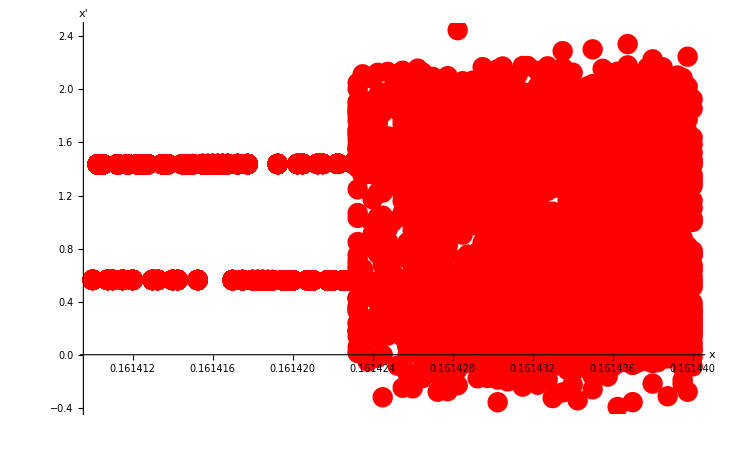

```mathematica
bifurcation[0.16141,0.16144,120,100,50,0.02]
```

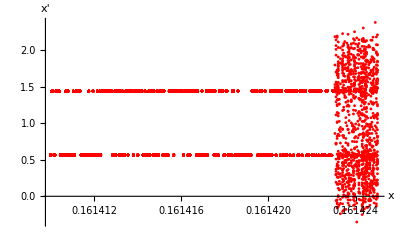

```mathematica
bifurcation[0.16141,0.161425,300,100,50,0.005]
```

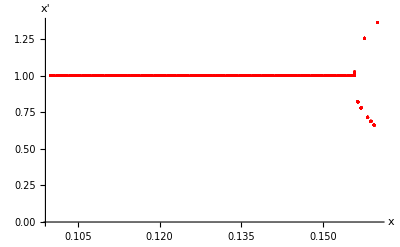

```mathematica
bifurcation[0.10,0.16,100,100,50,0.005]
```

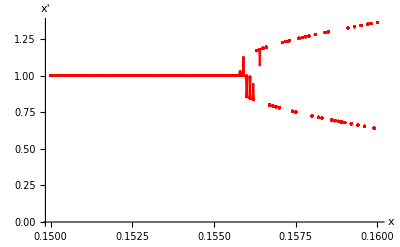

```mathematica
bifurcation[0.15,0.16,100,100,50,0.005]
```

```mathematica
bifurcation[0.155,0.156,200,100,50,0.005]
```

```mathematica
?gg
?baseList
?fX
?tableListX
```

Global`gg

gg[{prevStartValues_,d_}]:=({{X1[T],X2[T],X3[T],X4[T],X5[T],X6[T]},d}/.calcSol[d,T,prevStartValues])⟦1⟧

Global`baseList

baseList[d$_]:=Drop[NestList[gg,{startValuesFromStatic⟦All,2⟧,d$},50+100],100]

Global`fX

fX[{x_,d_}]:=(xElement=x⟦1⟧;{d,x⟦1⟧})

Global`tableListX

tableListX={{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.1614,1.43379},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161402,1.43418},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565408},{0.161405,0.565407},{0.161405,0.565408},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565408},{0.161405,0.565408},{0.161405,0.565407},{0.161405,0.565408},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565407},{0.161405,0.565408},{0.161405,0.565407},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.161407,1.43503},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564492},{0.16141,0.564492},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564491},{0.16141,0.564492},{0.16141,0.564491},{0.16141,0.564491},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161413,1.43603},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161415,1.43661},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.161418,0.56271},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561854},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.16142,0.561855},{0.161423,0.560405},{0.161423,0.560405},{0.161423,0.560405},{0.161423,0.560405},{0.161423,0.560405},{0.161423,0.560405},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560405},{0.161423,0.560405},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560404},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560403},{0.161423,0.560404},{0.161425,1.48304},{0.161425,1.56419},{0.161425,0.821111},{0.161425,0.182369},{0.161425,0.60919},{0.161425,1.92802},{0.161425,0.910168},{0.161425,1.94532},{0.161425,0.507095},{0.161425,0.00149184},{0.161425,0.3836},{0.161425,0.819803},{0.161425,1.25498},{0.161425,1.60682},{0.161425,1.83446},{0.161425,1.10541},{0.161425,1.23571},{0.161425,0.157881},{0.161425,0.74627},{0.161425,1.84701},{0.161425,1.59642},{0.161425,1.72601},{0.161425,1.47359},{0.161425,1.6949},{0.161425,1.48136},{0.161425,1.58155},{0.161425,0.440233},{0.161425,0.469458},{0.161425,1.72309},{0.161425,1.78785},{0.161425,1.11571},{0.161425,0.805363},{0.161425,2.20605},{0.161425,1.00442},{0.161425,0.47929},{0.161425,0.447982},{0.161425,0.760815},{0.161425,0.557794},{0.161425,0.0325936},{0.161425,0.493107},{0.161425,0.223822},{0.161425,0.46105},{0.161425,1.05977},{0.161425,1.53822},{0.161425,-0.0160247},{0.161425,0.723703},{0.161425,1.13239},{0.161425,1.71952},{0.161425,2.06832},{0.161425,0.369367},{0.161425,0.308161},{0.161428,-0.00558108},{0.161428,0.719196},{0.161428,0.0910001},{0.161428,1.30729},{0.161428,1.46351},{0.161428,1.7573},{0.161428,0.0723595},{0.161428,1.94291},{0.161428,1.41767},{0.161428,-0.0474904},{0.161428,0.976909},{0.161428,0.450726},{0.161428,0.803931},{0.161428,1.56937},{0.161428,0.697215},{0.161428,0.258251},{0.161428,-0.161074},{0.161428,1.33552},{0.161428,1.66925},{0.161428,1.4764},{0.161428,0.152473},{0.161428,1.5226},{0.161428,2.00356},{0.161428,1.73328},{0.161428,0.458097},{0.161428,-0.0129287},{0.161428,1.27466},{0.161428,0.263802},{0.161428,1.90722},{0.161428,1.91059},{0.161428,0.238705},{0.161428,0.511906},{0.161428,0.358241},{0.161428,1.01659},{0.161428,1.41838},{0.161428,1.47126},{0.161428,1.75575},{0.161428,1.04333},{0.161428,0.961753},{0.161428,0.89552},{0.161428,0.749351},{0.161428,0.595941},{0.161428,0.562889},{0.161428,0.560499},{0.161428,0.560026},{0.161428,0.559662},{0.161428,0.559308},{0.161428,0.55895},{0.161428,0.558576},{0.161428,0.558173},{0.161428,0.557723},{0.16143,1.46997},{0.16143,1.75984},{0.16143,1.92041},{0.16143,2.04391},{0.16143,0.365108},{0.16143,0.0332052},{0.16143,-0.00422585},{0.16143,0.387249},{0.16143,1.01216},{0.16143,0.333443},{0.16143,2.10853},{0.16143,1.57638},{0.16143,0.509831},{0.16143,0.405795},{0.16143,0.594447},{0.16143,0.551733},{0.16143,0.543175},{0.16143,0.514832},{0.16143,0.656255},{0.16143,1.7235},{0.16143,0.300537},{0.16143,0.320867},{0.16143,1.59118},{0.16143,0.435503},{0.16143,-0.00985385},{0.16143,0.639014},{0.16143,0.594034},{0.16143,0.489093},{0.16143,0.415053},{0.16143,1.48373},{0.16143,1.78746},{0.16143,1.07679},{0.16143,1.37842},{0.16143,1.95322},{0.16143,0.988381},{0.16143,0.930101},{0.16143,0.81868},{0.16143,0.643307},{0.16143,0.567619},{0.16143,0.560628},{0.16143,0.559756},{0.16143,0.559198},{0.16143,0.558643},{0.16143,0.55805},{0.16143,0.557384},{0.16143,0.556593},{0.16143,0.555589},{0.16143,0.554203},{0.16143,0.552065},{0.16143,0.548134},{0.16143,0.538043},{0.161433,0.680812},{0.161433,-0.0654235},{0.161433,0.259659},{0.161433,-0.169632},{0.161433,0.631467},{0.161433,0.963964},{0.161433,0.0911878},{0.161433,1.59753},{0.161433,1.92214},{0.161433,1.99435},{0.161433,1.48526},{0.161433,0.880006},{0.161433,1.48695},{0.161433,1.43471},{0.161433,1.66769},{0.161433,0.518374},{0.161433,0.999874},{0.161433,1.68171},{0.161433,2.06627},{0.161433,1.09707},{0.161433,1.02664},{0.161433,1.7365},{0.161433,1.33535},{0.161433,1.64667},{0.161433,0.0353609},{0.161433,0.632382},{0.161433,-0.167315},{0.161433,0.598158},{0.161433,0.410815},{0.161433,0.0989497},{0.161433,0.607785},{0.161433,0.155336},{0.161433,1.42847},{0.161433,1.70551},{0.161433,2.03216},{0.161433,1.7058},{0.161433,-0.0489097},{0.161433,1.9238},{0.161433,1.22536},{0.161433,1.42534},{0.161433,1.45355},{0.161433,1.47108},{0.161433,1.72909},{0.161433,0.168449},{0.161433,0.619685},{0.161433,0.335701},{0.161433,0.624516},{0.161433,0.24747},{0.161433,0.0642897},{0.161433,0.631166},{0.161433,0.407471},{0.161435,0.554637},{0.161435,1.71793},{0.161435,1.07758},{0.161435,1.84974},{0.161435,1.81957},{0.161435,1.32035},{0.161435,1.69792},{0.161435,0.284488},{0.161435,0.504573},{0.161435,0.140428},{0.161435,0.248422},{0.161435,0.0989475},{0.161435,-0.260696},{0.161435,1.19913},{0.161435,1.78588},{0.161435,1.12844},{0.161435,1.97482},{0.161435,1.56624},{0.161435,1.57952},{0.161435,1.46767},{0.161435,1.86635},{0.161435,0.856551},{0.161435,2.30217},{0.161435,0.620664},{0.161435,0.302641},{0.161435,1.42465},{0.161435,1.61631},{0.161435,1.78442},{0.161435,-0.160667},{0.161435,1.98849},{0.161435,0.161829},{0.161435,-0.0232511},{0.161435,0.0018801},{0.161435,1.32008},{0.161435,1.76625},{0.161435,0.366879},{0.161435,0.235151},{0.161435,0.23595},{0.161435,1.98131},{0.161435,1.1034},{0.161435,0.139564},{0.161435,1.3452},{0.161435,1.76335},{0.161435,1.70343},{0.161435,2.03984},{0.161435,1.58198},{0.161435,1.80026},{0.161435,1.38682},{0.161435,1.6897},{0.161435,1.80084},{0.161435,0.105628},{0.161438,1.08759},{0.161438,1.24989},{0.161438,1.4046},{0.161438,1.43782},{0.161438,1.44086},{0.161438,1.44211},{0.161438,1.4434},{0.161438,1.44502},{0.161438,1.44734},{0.161438,1.45137},{0.161438,1.46123},{0.161438,1.52985},{0.161438,1.30655},{0.161438,1.63842},{0.161438,0.946172},{0.161438,0.263006},{0.161438,0.387189},{0.161438,0.393958},{0.161438,0.166032},{0.161438,0.519272},{0.161438,1.01213},{0.161438,1.04851},{0.161438,1.1287},{0.161438,1.29179},{0.161438,1.41958},{0.161438,1.43902},{0.161438,1.44109},{0.161438,1.44229},{0.161438,1.44361},{0.161438,1.4453},{0.161438,1.44779},{0.161438,1.45226},{0.161438,1.4641},{0.161438,1.58662},{0.161438,0.543189},{0.161438,0.43152},{0.161438,2.01096},{0.161438,0.35531},{0.161438,2.09647},{0.161438,2.02199},{0.161438,0.819354},{0.161438,0.24052},{0.161438,0.195889},{0.161438,1.14254},{0.161438,1.55526},{0.161438,1.95039},{0.161438,1.68224},{0.161438,0.493901},{0.161438,0.947508},{0.161438,1.74116},{0.161438,1.42348},{0.16144,0.233128},{0.16144,0.640616},{0.16144,0.34178},{0.16144,0.674432},{0.16144,0.541065},{0.16144,1.30842},{0.16144,1.52162},{0.16144,1.01042},{0.16144,0.74909},{0.16144,0.645499},{0.16144,0.390526},{0.16144,1.63679},{0.16144,1.35559},{0.16144,1.46735},{0.16144,0.592796},{0.16144,0.560631},{0.16144,0.783603},{0.16144,0.209814},{0.16144,0.320456},{0.16144,1.92758},{0.16144,1.16192},{0.16144,0.0855599},{0.16144,0.0444085},{0.16144,-0.0881009},{0.16144,0.259946},{0.16144,1.27332},{0.16144,1.10674},{0.16144,1.32016},{0.16144,1.43375},{0.16144,1.44506},{0.16144,1.44758},{0.16144,1.45215},{0.16144,1.46398},{0.16144,1.58466},{0.16144,0.771008},{0.16144,0.291692},{0.16144,0.510833},{0.16144,1.85481},{0.16144,0.251188},{0.16144,0.350316},{0.16144,0.153863},{0.16144,0.26193},{0.16144,1.0278},{0.16144,0.319725},{0.16144,0.131321},{0.16144,0.178863},{0.16144,-0.0156583},{0.16144,1.00115},{0.16144,0.759357},{0.16144,0.173103},{0.16144,0.0347126},{0.161443,1.60066},{0.161443,0.197955},{0.161443,0.240636},{0.161443,1.78341},{0.161443,2.14075},{0.161443,2.11708},{0.161443,0.287971},{0.161443,0.0219791},{0.161443,1.78863},{0.161443,1.7062},{0.161443,1.43312},{0.161443,0.655412},{0.161443,1.45975},{0.161443,0.853737},{0.161443,1.78402},{0.161443,0.985849},{0.161443,1.82607},{0.161443,1.94496},{0.161443,0.274214},{0.161443,0.264866},{0.161443,0.497702},{0.161443,0.957926},{0.161443,1.9255},{0.161443,1.91317},{0.161443,0.0521817},{0.161443,0.454784},{0.161443,0.405519},{0.161443,0.757955},{0.161443,0.176972},{0.161443,1.89668},{0.161443,1.67661},{0.161443,0.350614},{0.161443,1.93836},{0.161443,1.74209},{0.161443,0.41207},{0.161443,0.155412},{0.161443,0.889363},{0.161443,-0.178877},{0.161443,0.23081},{0.161443,0.676244},{0.161443,0.646594},{0.161443,0.820013},{0.161443,1.9232},{0.161443,0.282029},{0.161443,1.09977},{0.161443,0.464224},{0.161443,0.191444},{0.161443,1.3805},{0.161443,1.70303},{0.161443,1.52223},{0.161443,0.338424},{0.161445,1.02533},{0.161445,0.397451},{0.161445,0.115756},{0.161445,0.122323},{0.161445,-0.0796239},{0.161445,0.657788},{0.161445,1.98133},{0.161445,1.182},{0.161445,1.12024},{0.161445,1.28318},{0.161445,1.41763},{0.161445,1.43949},{0.161445,1.44229},{0.161445,1.44427},{0.161445,1.44685},{0.161445,1.45112},{0.161445,1.46129},{0.161445,1.53271},{0.161445,1.15521},{0.161445,0.198658},{0.161445,0.771659},{0.161445,1.75196},{0.161445,1.78445},{0.161445,-0.0406879},{0.161445,0.695259},{0.161445,0.738073},{0.161445,0.239068},{0.161445,0.116843},{0.161445,0.268259},{0.161445,1.6067},{0.161445,2.10716},{0.161445,1.84165},{0.161445,1.34038},{0.161445,0.120966},{0.161445,0.440542},{0.161445,0.225598},{0.161445,0.34778},{0.161445,1.52633},{0.161445,1.53008},{0.161445,1.82892},{0.161445,1.88428},{0.161445,2.03221},{0.161445,0.393719},{0.161445,0.231251},{0.161445,1.67922},{0.161445,0.291184},{0.161445,2.34995},{0.161445,-0.0812371},{0.161445,0.950787},{0.161445,1.80852},{0.161445,2.06846},{0.161448,0.0796889},{0.161448,0.288208},{0.161448,0.824032},{0.161448,1.02315},{0.161448,1.07084},{0.161448,1.18224},{0.161448,1.35825},{0.161448,1.43341},{0.161448,1.44121},{0.161448,1.44346},{0.161448,1.44593},{0.161448,1.4497},{0.161448,1.45761},{0.161448,1.49321},{0.161448,1.44658},{0.161448,0.300878},{0.161448,0.0143792},{0.161448,1.79038},{0.161448,0.356304},{0.161448,2.01385},{0.161448,0.220651},{0.161448,0.607841},{0.161448,0.372684},{0.161448,0.252569},{0.161448,0.331176},{0.161448,1.62265},{0.161448,1.89922},{0.161448,0.0206157},{0.161448,0.192324},{0.161448,1.49138},{0.161448,1.99886},{0.161448,1.73579},{0.161448,0.383531},{0.161448,1.83622},{0.161448,0.132004},{0.161448,1.58091},{0.161448,1.48936},{0.161448,1.15454},{0.161448,1.02607},{0.161448,1.07449},{0.161448,1.19127},{0.161448,1.36654},{0.161448,1.43452},{0.161448,1.44137},{0.161448,1.44358},{0.161448,1.4461},{0.161448,1.44999},{0.161448,1.45838},{0.161448,1.49948},{0.161448,2.35202},{0.161448,1.11711},{0.16145,0.596655},{0.16145,0.623712},{0.16145,1.64479},{0.16145,0.640157},{0.16145,-0.189031},{0.16145,0.826161},{0.16145,1.84051},{0.16145,1.08197},{0.16145,1.16497},{0.16145,1.34216},{0.16145,1.43113},{0.16145,1.44128},{0.16145,1.44387},{0.16145,1.44673},{0.16145,1.45135},{0.16145,1.46255},{0.16145,1.55597},{0.16145,1.86197},{0.16145,1.17704},{0.16145,1.54612},{0.16145,0.954038},{0.16145,0.40094},{0.16145,0.573122},{0.16145,0.155574},{0.16145,-0.041266},{0.16145,1.7649},{0.16145,1.17897},{0.16145,1.69509},{0.16145,0.192234},{0.16145,0.473659},{0.16145,0.235397},{0.16145,1.77262},{0.16145,1.98372},{0.16145,0.247237},{0.16145,1.79371},{0.16145,0.879634},{0.16145,0.510109},{0.16145,-0.0482958},{0.16145,2.21242},{0.16145,1.90703},{0.16145,1.96987},{0.16145,1.80226},{0.16145,1.3179},{0.16145,1.49284},{0.16145,1.70458},{0.16145,0.724582},{0.16145,0.337413},{0.16145,-0.112699},{0.16145,1.35556},{0.16145,1.8287},{0.16145,1.27624}}